```mathematica
fsz=22;16;
(*path=NotebookDirectory[]<>"figures/"*)
fontFamilyPB="Latin Modern Math";"Helvetica";
fontFamily="Times New Roman";FontSize->24;

SetOptions[Plot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogLinearPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogLogPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[Graphics,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];

PPlot[sol_]:= Module[{lineStyle,pltStl,thickness},
lineStyle=Dashing[{1,0}];Automatic;xRPlotMin=0;ar=1;gridLines=Automatic;imSz=400;
pltStl={{lineStyle,Blue,Thickness[thickness=.013/2]},{lineStyle,RGBColor[0.7,0.3,0.0],Thickness[thickness]},{lineStyle,RGBColor[0.9,0.5,0.6],Thickness[thickness]},{lineStyle,Brown,Thickness[thickness]},{lineStyle,Black,Thickness[thickness]}};
Plot[Evaluate[{O2'[t],O2[t]}/.sol],{t,0,Tmax}(*,PlotRange->All*),(*PlotLegends->Placed[{"g GL_ij","g (H-ω)^-1","ψ_j"},{.65,.5}],*)PlotRange->{{0,Tmax},{0,1}},AspectRatio->1,(*ImageSize->250,*)FrameLabel->{"Time","Amount"},
PlotLegends->Placed[{Style["O_2'",FontSize->fsz,FontFamily->fontFamily],Style["O_2",FontSize->fsz,FontFamily->fontFamily],Style["CO_2",FontSize->fsz,FontFamily->fontFamily]},{0.45,0.85}],ImageSize->imSz,Axes->None,PlotStyle->pltStl,Frame->True,BaseStyle->{FontFamily->"Times New Roman",FontSize->fsz},FrameStyle->Thick,FrameTicksStyle->Black,LabelStyle->Black,GridLines->gridLines,AspectRatio->ar
]
];
```

```mathematica
Clear[F,B,O2,B0,C0,Func,M];
```

```mathematica
Func:=Module[{f,g,eqs,BC,DEq,solg,sol,rts,Evs},
f=HeavisideTheta[R[t]-R0]α A[t](R[t]-R0);
g=ϵ A[t]R[t]HeavisideTheta[R1-R[t]]+ϵ A[t] R1 HeavisideTheta[R[t]-R1];

eqs={R'[t] == -f-g+σ1,
G'[t]== ((1-ξ)ω R[t] - a1) G[t],
H'[t]==  ((1-ψ)Ω CH[t] - a2) H[t],
L'[t]== f - β B[t] L[t]+ξ ω R[t] G[t],
CO'[t]==μ O2[t] g + γ λ O2[t] CH[t] F[t]+ψ Ω CH[t] H[t],
CH'[t] == κ β B[t] L[t] - γ O2[t] CH[t] F[t],
O2'[t] == -(μ O2[t] g + γ λ O2[t] CH[t] F[t])+σ2,
A'[t] == (1-μ)O2[t]g - s A[t],
B'[t]==((1-κ) β L[t] -u) B[t],
F'[t] == ((1-λ)γ O2[t] CH[t]-ν)F[t]};
BC = {R[0]==RI,L[0]==0,CO[0]==0,CH[0]==0,A[0]==A0,B[0]==B0,F[0]==C0,O2[0]==O20,G[0]==G0,H[0]==H0};
Evs={WhenEvent[O2'[t]==0,Sow[t]]};
DEq = Flatten[{eqs,BC,Evs}];
solg=Reap[NDSolve[DEq,{A,B,F,O2',CH',L',CO',R',O2,CH,L,CO,R,G,H},{t,0,Tmax}]];
sol =solg[[1]];
rts = solg[[2]];
{First[sol],First[rts]}
(*{Plot[Evaluate[{F[t],B[t],A[t]}/.sol],{t,0,Tmax},PlotRange->PR,PlotLegends->{"F","B","A"}],
Plot[Evaluate[{O2'[t],CH'[t],L'[t],CO'[t],R'[t]}/.sol],{t,0,Tmax},PlotRange->All,PlotLegends->{"O2","CH4","Lac","CO2","R"}],
Plot[Evaluate[{O2[t],CH[t],L[t],CO[t],R[t]}/.sol],{t,0,Tmax},PlotRange->All,PlotLegends->{"O2","CH4","Lac","CO2","R"}]
};*)
]
```

```mathematica
R0=2.5;
R1=1;

a2 = 1.5;
a1=1.5; (* 0.1  *)
s=0.1;
ν=0.1;
u=0.1;

λ=0.5; 
κ=0.5;
μ=0.5;
ξ=0.5; (* 0.5 *)
ψ=0.5;

A0=1.;
H0=1; (*1? *)
G0=1;
B0=1;
C0=1;

β=0.5; 
α=0.5; (* 0.5 *)
ω=0.02; (* 0.02 *)
Ω=0.02;
ϵ=0.5;
γ=0.5;
```

#### Oscillation qualitative analysis

```mathematica
RI=10;
O20=1;
σ1 = 1; (* resource rate  0.8*)

Table[
σ2 = 0.1+i; (* oxygen rate 0.15 *)
If[i<0.09,cut=7;Tmax=400;,cut=7;Tmax=550];
{sol,rts}  = Func;
tx = 97;

Tper=rts[[6;;cut]]-RotateRight[rts,2][[6;;cut]];
m = Mean[Tper];
st =StandardDeviation[Tper];
{σ2,m}
,{i,0,0.1,0.0005}]
```

{{0.1,94.2691},{0.1005,93.3683},{0.101,92.4866},{0.1015,91.6234},{0.102,90.7782},{0.1025,89.9503},{0.103,89.1393},{0.1035,88.3447},{0.104,87.5655},{0.1045,86.8017},{0.105,86.0527},{0.1055,85.318},{0.106,84.5971},{0.1065,83.8897},{0.107,83.1954},{0.1075,82.5137},{0.108,81.8442},{0.1085,81.1869},{0.109,80.5412},{0.1095,79.9067},{0.11,79.2832},{0.1105,78.6704},{0.111,78.0681},{0.1115,77.476},{0.112,76.894},{0.1125,76.3215},{0.113,75.7585},{0.1135,75.2048},{0.114,74.6601},{0.1145,74.1243},{0.115,73.5972},{0.1155,73.0785},{0.116,72.5681},{0.1165,72.066},{0.117,71.5716},{0.1175,71.0852},{0.118,70.6065},{0.1185,70.1354},{0.119,69.6715},{0.1195,69.215},{0.12,68.7656},{0.1205,68.3232},{0.121,67.8877},{0.1215,67.459},{0.122,67.037},{0.1225,66.6215},{0.123,66.2125},{0.1235,65.8099},{0.124,65.4135},{0.1245,65.0234},{0.125,64.6393},{0.1255,64.2612},{0.126,63.8891},{0.1265,63.5228},{0.127,63.1622},{0.1275,62.8074},{0.128,62.4582},{0.1285,62.1144},{0.129,61.7762},{0.1295,61.4434},{0.13,61.1159},{0.1305,60.7936},{0.131,60.4766},{0.1315,60.1647},{0.132,59.8579},{0.1325,59.5562},{0.133,59.2594},{0.1335,58.9675},{0.134,58.6805},{0.1345,58.3982},{0.135,58.1208},{0.1355,57.848},{0.136,57.5798},{0.1365,57.3163},{0.137,57.0573},{0.1375,56.8027},{0.138,56.5526},{0.1385,56.3069},{0.139,56.0655},{0.1395,55.8284},{0.14,55.5955},{0.1405,55.3667},{0.141,55.1421},{0.1415,54.9216},{0.142,54.7051},{0.1425,54.4925},{0.143,54.2839},{0.1435,54.0791},{0.144,53.8781},{0.1445,53.6808},{0.145,53.4873},{0.1455,53.2974},{0.146,53.111},{0.1465,52.9283},{0.147,52.7489},{0.1475,52.573},{0.148,52.4005},{0.1485,52.2313},{0.149,52.0653},{0.1495,51.9025},{0.15,51.7429},{0.1505,51.5864},{0.151,51.4329},{0.1515,51.2823},{0.152,51.1347},{0.1525,50.99},{0.153,50.8481},{0.1535,50.7089},{0.154,50.5725},{0.1545,50.4387},{0.155,50.3075},{0.1555,50.1788},{0.156,50.0527},{0.1565,49.929},{0.157,49.8077},{0.1575,49.6887},{0.158,49.572},{0.1585,49.4575},{0.159,49.3453},{0.1595,49.2351},{0.16,49.1271},{0.1605,49.0211},{0.161,48.917},{0.1615,48.8149},{0.162,48.7147},{0.1625,48.6163},{0.163,48.5198},{0.1635,48.4249},{0.164,48.3318},{0.1645,48.2403},{0.165,48.1504},{0.1655,48.0621},{0.166,47.9752},{0.1665,47.8899},{0.167,47.806},{0.1675,47.7234},{0.168,47.6422},{0.1685,47.5623},{0.169,47.4836},{0.1695,47.4061},{0.17,47.3298},{0.1705,47.2546},{0.171,47.1804},{0.1715,47.1073},{0.172,47.0353},{0.1725,46.9641},{0.173,46.8939},{0.1735,46.8246},{0.174,46.7561},{0.1745,46.6885},{0.175,46.6216},{0.1755,46.5554},{0.176,46.49},{0.1765,46.4252},{0.177,46.3611},{0.1775,46.2975},{0.178,46.2345},{0.1785,46.1721},{0.179,46.1102},{0.1795,46.0488},{0.18,45.9879},{0.1805,45.9274},{0.181,45.8673},{0.1815,45.8076},{0.182,45.7482},{0.1825,45.6893},{0.183,45.6306},{0.1835,45.5722},{0.184,45.5142},{0.1845,45.4565},{0.185,45.399},{0.1855,45.3418},{0.186,45.2848},{0.1865,45.2281},{0.187,45.1717},{0.1875,45.1155},{0.188,45.0597},{0.1885,45.0041},{0.189,44.9487},{0.1895,44.8937},{0.19,44.839},{0.1905,44.7847},{0.191,44.7307},{0.1915,44.6772},{0.192,44.624},{0.1925,44.5714},{0.193,44.5193},{0.1935,44.4678},{0.194,44.4169},{0.1945,44.3664},{0.195,44.317},{0.1955,44.2684},{0.196,44.2204},{0.1965,44.1736},{0.197,44.1276},{0.1975,44.083},{0.198,44.0394},{0.1985,43.9971},{0.199,43.9558},{0.1995,43.9159},{0.2,42.44}}

```mathematica
σ2 = 0.19; (* oxygen rate 0.15 *)
Tmax =550;
Func = sol;
αo = γ λ;
g=ϵ A[t]R[t]HeavisideTheta[R1-R[t]]+ϵ A[t] R1 HeavisideTheta[R[t]-R1];
f=HeavisideTheta[R[t]-R0]α A[t](R[t]-R0);
```

#### O2’[t]

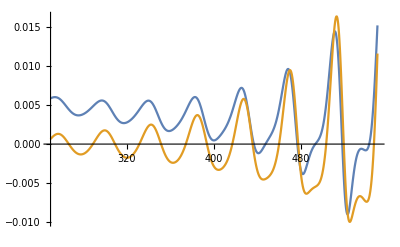

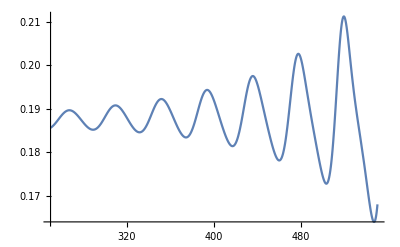

```mathematica
Plot[Evaluate[{- αo O2[t] (CH[t] F[t])^2+ σ2 CH[t] F[t]+(*O2[t]CH[t] F'[t],*)O2[t]CH'[t] F[t],-O2''[t]/αo}/.sol],{t,250,Tmax},PlotLegends->Automatic]
Plot[{ γ λ O2[t] CH[t] F[t]}/.sol,{t,250,Tmax}]
```

#### CH’[t]

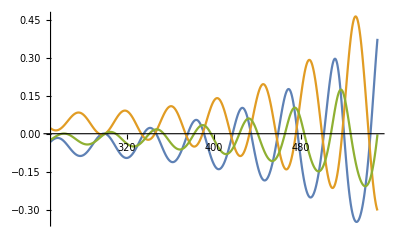

```mathematica
Plot[Evaluate[{O2[t]/Abs[O2[300]]-1,CH[t]/CH[300]-1,(L[t]/L[300]-1)}/.sol],{t,250,Tmax},PlotLegends->Automatic]
```

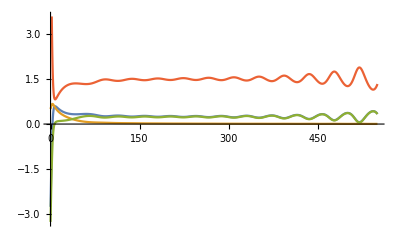

```mathematica
Plot[Evaluate[{-f+σ1,g,R'[t],A[t](R[t]-R0)}/.sol],{t,0,Tmax},PlotLegends->Automatic]
```

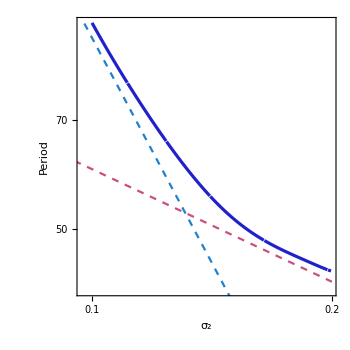

```mathematica
pper={94.32.8,93.42.7,92.52.6,91.62.6,90.82.5,90.02.4,89.12.3,88.32.2,87.62.2,86.82.1,86.12.0,85.31.9,84.61.9,83.91.8,83.21.7,82.51.7,81.81.6,81.21.6,80.51.5,79.91.5,79.31.4,78.71.4,78.11.3,77.51.3,76.91.2,76.31.2,75.81.2,75.21.1,74.71.1,74.11.1,73.61.0,73.11.0,72.61.0,72.10.9,71.60.9,71.10.9,70.60.9,70.10.8,69.70.8,69.20.8,68.80.8,68.30.8,67.90.8,67.50.7,67.00.7,66.60.7,66.20.7,65.80.7,65.40.7,65.00.7,64.60.7,64.30.7,63.90.6,63.50.6,63.20.6,62.80.6,62.50.6,62.10.6,61.80.6,61.40.6,61.10.6,60.80.6,60.50.6,60.20.6,59.90.6,59.60.6,59.30.6,59.00.6,58.70.6,58.40.6,58.10.6,57.80.6,57.60.5,57.30.5,57.10.5,56.80.5,56.60.5,56.30.5,56.10.5,55.80.5,55.60.5,55.40.5,55.10.5,54.90.5,54.70.5,54.50.5,54.30.5,54.10.5,53.90.5,53.70.5,53.50.5,53.30.5,53.10.5,52.90.5,52.70.4,52.60.4,52.40.4,52.20.4,52.10.4,51.90.4,51.70.4,51.60.4,51.40.4,51.30.4,51.10.4,51.00.4,50.80.4,50.70.4,50.60.4,50.440.35,50.310.34,50.180.34,50.050.33,49.930.32,49.810.32,49.690.31,49.570.30,49.460.30,49.350.29,49.240.28,49.130.28,49.020.27,48.920.26,48.810.25,48.710.25,48.620.24,48.520.23,48.420.23,48.330.22,48.240.21,48.150.21,48.060.20,47.980.19,47.890.19,47.810.18,47.720.17,47.640.16,47.560.16,47.480.15,47.410.14,47.330.13,47.250.12,47.180.12,47.110.11,47.040.10,46.960.09,46.890.08,46.820.07,46.760.06,46.690.04,46.6220.033,46.5550.020,46.4900.007,46.4250.007,46.3610.021,46.300.04,46.230.05,46.170.07,46.110.09,46.050.11,45.990.12,45.930.15,45.870.17,45.810.19,45.750.21,45.690.24,45.630.27,45.570.30,45.510.33,45.50.4,45.40.4,45.30.4,45.30.5,45.20.5,45.20.6,45.10.6,45.10.6,45.00.7,44.90.8,44.90.8,44.80.9,44.80.9,44.71.0,44.71.1,44.61.2,44.61.2,44.51.3,44.51.4,44.41.5,44.41.7,44.31.8,44.31.9,44.22.1,44.22.3,44.12.5,44.12.7,44.03.1,44.03.5,44.4.,44.6.,42.43.1};
pper2={{0.1,94.26909732169327},{0.1005,93.36826155209161},{0.101,92.48656432287557},{0.1015,91.62344843573578},{0.10200000000000001,90.7781889200433},{0.10250000000000001,89.95030212533996},{0.10300000000000001,89.13927716360902},{0.10350000000000001,88.34466071883551},{0.10400000000000001,87.5655381635535},{0.10450000000000001,86.8017409186638},{0.10500000000000001,86.0526764199216},{0.10550000000000001,85.31796563623146},{0.10600000000000001,84.59711453033887},{0.10650000000000001,83.88970537028531},{0.10700000000000001,83.1953525739226},{0.10750000000000001,82.51366415037086},{0.10800000000000001,81.8442045227678},{0.10850000000000001,81.1869143665107},{0.10900000000000001,80.54115799596207},{0.1095,79.9066707634075},{0.11,79.28319369570454},{0.1105,78.67040043214017},{0.111,78.06809356403112},{0.1115,77.47600654516327},{0.112,76.89402229247058},{0.1125,76.3214854273375},{0.113,75.758493428387},{0.1135,75.20478559909527},{0.114,74.66012519246823},{0.1145,74.12431906170701},{0.115,73.59718666393562},{0.1155,73.07852195367445},{0.116,72.56805713198929},{0.1165,72.06599935151714},{0.117,71.5715860703037},{0.11750000000000001,71.08516449959852},{0.11800000000000001,70.60645239581731},{0.11850000000000001,70.13536301572015},{0.11900000000000001,69.67154129306289},{0.11950000000000001,69.21501195053057},{0.12000000000000001,68.76560102130566},{0.12050000000000001,68.32321787937576},{0.12100000000000001,67.88771717232237},{0.12150000000000001,67.45901653078114},{0.122,67.03701082131116},{0.1225,66.62152640560491},{0.123,66.21250854211422},{0.1235,65.80994629515384},{0.124,65.41352913512941},{0.1245,65.02338422846762},{0.125,64.63926556988312},{0.1255,64.26124296732227},{0.126,63.88909478430472},{0.1265,63.52280236067512},{0.127,63.162243242312805},{0.1275,62.807391945296345},{0.128,62.45815306393722},{0.1285,62.11442934600033},{0.129,61.776197040324845},{0.1295,61.44336304905834},{0.13,61.115859710346115},{0.1305,60.79362672737739},{0.131,60.47661089310307},{0.1315,60.16472673562844},{0.132,59.857936765017655},{0.1325,59.556178704593805},{0.133,59.25939880668887},{0.1335,58.96749843418749},{0.134,58.68047120892354},{0.1345,58.39824816501859},{0.135,58.1207758316374},{0.1355,57.84798677161947},{0.136,57.57984366829061},{0.1365,57.316276361039236},{0.137,57.057254007411686},{0.1375,56.80271398312326},{0.138,56.552610292016695},{0.1385,56.30688008580256},{0.139,56.06548741256719},{0.1395,55.82835539058876},{0.14,55.59545399407198},{0.1405,55.36673465041079},{0.14100000000000001,55.142117923003234},{0.14150000000000001,54.92160145818446},{0.14200000000000002,54.70505982008492},{0.14250000000000002,54.49250729589356},{0.14300000000000002,54.2838531194157},{0.14350000000000002,54.079069205356355},{0.14400000000000002,53.87806337827936},{0.14450000000000002,53.68081790211682},{0.14500000000000002,53.48727043465077},{0.14550000000000002,53.29736453082444},{0.14600000000000002,53.111031355534436},{0.14650000000000002,52.928266483312875},{0.14700000000000002,52.74893819887949},{0.14750000000000002,52.573022805411306},{0.14800000000000002,52.400486643101296},{0.14850000000000002,52.23126743254721},{0.14900000000000002,52.06529292052359},{0.14950000000000002,51.902521779156274},{0.15000000000000002,51.74289648927875},{0.15050000000000002,51.58636127883745},{0.15100000000000002,51.43285441876306},{0.15150000000000002,51.28233179439344},{0.15200000000000002,51.13472422579312},{0.1525,50.98999280503256},{0.153,50.84808378735341},{0.1535,50.70892598782596},{0.154,50.57250126035251},{0.1545,50.43868777546171},{0.155,50.30749357945838},{0.1555,50.17884107022194},{0.156,50.05269061515004},{0.1565,49.928985094174024},{0.157,49.80768077420737},{0.1575,49.68868351249145},{0.158,49.57199369149802},{0.1585,49.45754100605094},{0.159,49.34526655420548},{0.1595,49.23513512065628},{0.16,49.127074763382},{0.1605,49.021055184443796},{0.161,48.91701653153624},{0.1615,48.81492395679218},{0.162,48.71472672261193},{0.1625,48.61634213450678},{0.163,48.51976688667286},{0.1635,48.42493305031928},{0.164,48.331802624549745},{0.1645,48.24030510478987},{0.165,48.15040119431247},{0.1655,48.06209275641307},{0.166,47.97524396200969},{0.1665,47.88991224262745},{0.167,47.80597244511205},{0.1675,47.723416110361974},{0.168,47.642198100658085},{0.1685,47.56225033916522},{0.169,47.48356513489875},{0.1695,47.40608515805943},{0.17,47.32977376357417},{0.1705,47.25458153160586},{0.171,47.18042165457872},{0.1715,47.10734393932454},{0.17200000000000001,47.03527171612988},{0.1725,46.964130522361316},{0.173,46.89393344249999},{0.1735,46.824599454772745},{0.174,46.75614275066978},{0.1745,46.688486539158866},{0.175,46.62155977993913},{0.1755,46.55539286431791},{0.176,46.489971189266136},{0.1765,46.42517996803776},{0.177,46.361051129081424},{0.1775,46.29751449379563},{0.178,46.23454775102817},{0.1785,46.172138407301034},{0.179,46.11024650286135},{0.1795,46.04883083952862},{0.18,45.98789742897127},{0.1805,45.927388392338685},{0.181,45.86732798576737},{0.1815,45.80760650962593},{0.182,45.7482311191015},{0.1825,45.68925631273422},{0.183,45.63060389844721},{0.1835,45.57222835410969},{0.184,45.51419617279036},{0.1845,45.45645205959072},{0.185,45.398981759122314},{0.1855,45.34178433610845},{0.186,45.28478151651506},{0.1865,45.22810472896629},{0.187,45.171727537350336},{0.1875,45.11552479861363},{0.188,45.05965468039621},{0.1885,45.004051218188685},{0.189,44.94872940693229},{0.1895,44.8937289263918},{0.19,44.8390343573126},{0.1905,44.784684122103826},{0.191,44.73068330760376},{0.1915,44.67718642437167},{0.192,44.624027204184436},{0.1925,44.571441961522694},{0.193,44.51934257365673},{0.1935,44.46780073065123},{0.194,44.41685919057109},{0.1945,44.36644879322792},{0.195,44.31704974184897},{0.1955,44.26838988372874},{0.196,44.22035916099703},{0.1965,44.173591056435484},{0.197,44.12762127814681},{0.1975,44.08301182035952},{0.198,44.03937271166883},{0.1985,43.99710495125334},{0.199,43.9557940155698},{0.1995,43.9158915840268}};
lineStyle=Dashing[{1,0}];Automatic;xRPlotMin=0;ar=1;gridLines=Automatic;imSz=400;
pltStl={{lineStyle,RGBColor[0.13,0.13,0.8],Thickness[thickness=.013/2]},{lineStyle,RGBColor[0.7,0.3,0.0],Thickness[thickness]},{lineStyle,RGBColor[0.9,0.5,0.6],Thickness[thickness]},{lineStyle,Brown,Thickness[thickness]},{lineStyle,Black,Thickness[thickness]}};
p1=ListLogLogPlot[pper2,Joined->True,PlotRange->All,AspectRatio->1,ImageSize->350,FrameLabel->{"σ_2","Period"},
(*PlotLegends->Placed[{Style["O_2'",FontSize->fsz,FontFamily->fontFamily],Style["O_2",FontSize->fsz,FontFamily->fontFamily],Style["CO_2",FontSize->fsz,FontFamily->fontFamily]},{0.45,0.85}],*)Axes->None,PlotStyle->pltStl,Frame->True,BaseStyle->{FontFamily->"Times New Roman",FontSize->fsz},FrameStyle->Thick,FrameTicksStyle->Black,LabelStyle->Black,GridLines->gridLines,AspectRatio->ar,
Epilog->Line[{{0.1,50},{0.2,100}}]
];
Show[p1,LogLogPlot[{0.9x^{-2},19x^{-1/2}},{x,0.,0.2},PlotStyle->{{RGBColor[0.13,0.5,0.8],Dashed},{RGBColor[0.8,0.3,0.5],Dashed}},PlotLegends->Placed[{Style["~σ_2^-2",FontSize->fsz,FontFamily->fontFamily],Style["~σ_2^(-1/2)",FontSize->fsz,FontFamily->fontFamily]},{0.65,0.65}]]]
```

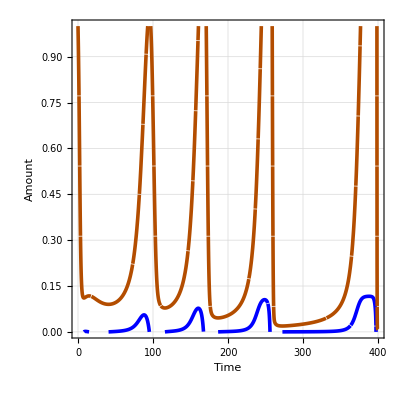

77.10.

```mathematica
RI=10;
O20=1;
σ1 = 1; (* resource rate  0.8*)
σ2 = 0.117; (* oxygen rate 0.15 *)
Tmax =400;
{sol,rts}  = Func;
tx = 97;
PPlot[sol]
Tper=rts[[6;;-3]]-RotateRight[rts,2][[6;;-3]];
Around[Mean[Tper],
StandardDeviation[Tper]]
```

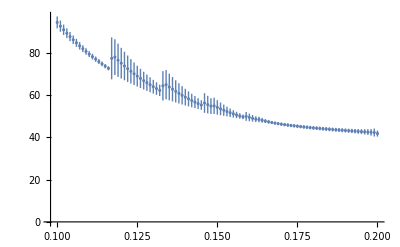

```mathematica
pper={94.32.8,92.52.6,90.82.5,89.12.3,87.62.2,86.12.0,84.61.9,83.21.7,81.81.6,80.51.5,79.31.4,78.11.3,76.91.2,75.81.2,74.71.1,73.61.0,72.61.0,77.10.,78.8.,76.8.,75.7.,74.7.,72.6.,71.6.,70.5.,69.5.,68.5.,67.4.,66.4.,64.83.5,63.93.2,63.03.0,62.22.7,64.7.,65.7.,64.6.,63.6.,62.5.,61.5.,60.4.,59.4.,58.4.,57.33.2,56.62.9,55.92.6,55.22.3,56.5.,55.4.,55.4.,55.4.,54.13.4,53.43.0,52.82.6,52.22.3,51.62.0,51.01.7,50.51.5,50.11.3,49.61.1,49.92.1,49.41.8,49.01.6,48.51.3,48.41.3,48.01.1,47.60.9,47.30.8,47.00.7,46.70.7,46.40.7,46.20.7,46.00.7,45.70.7,45.60.8,45.40.8,45.20.8,45.00.8,44.90.8,44.70.8,44.60.8,44.40.8,44.30.9,44.10.9,44.00.9,43.90.9,43.80.9,43.70.9,43.50.9,43.40.9,43.30.9,43.21.0,43.11.0,43.01.0,42.91.0,42.81.1,42.71.2,42.51.2,42.41.4,42.31.5,42.21.9,41.71.4};
ListPlot[pper,DataRange->{0.1,0.2}]
```

```mathematica
f1[t_] := O2'[t]/.sol

Reap[NDSolve[{1.09 x''[t]-0.05 x'[t]+1.1759 Sin[x[t]]==0,x[0]==Pi/3,x'[0]==0,WhenEvent[x[t]==0,Sow[t]]},x,{t,0,50}]][[2]]
```

{{1.59975,4.88823,8.22838,11.6339,15.1242,18.7282,22.4934,26.5081,30.9882,37.4065}}

```mathematica
Table[
i,{i,0,0.15,0.005}]
```

{0.,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105,0.11,0.115,0.12,0.125,0.13,0.135,0.14,0.145,0.15}

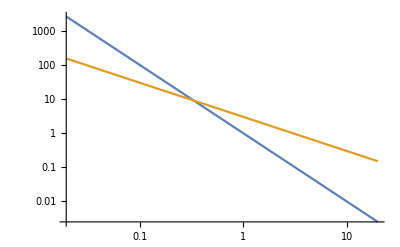

```mathematica
LogLogPlot[{x^(-2),3x^{-1}},{x,0,20}]
```

```mathematica
Solve[c*0.1^(-2)==94.26909732169327,c]
```

{{c→0.942691}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

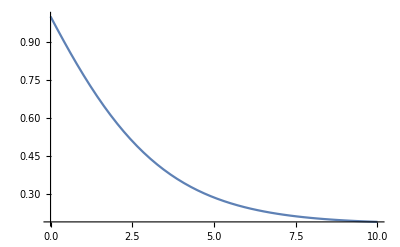

```mathematica
Plot[Evaluate[O2[t]/.DSolve[{O2'[t]==-.25 O2[t](-O2[t]+2.38)+0.1,O2[0]==1},O2[t],t][[1]]],{t,0,10}]
```

```mathematica
eqsapp={
CH'[t] == κ β B[t] L[t] - γ O2[t] CH[t] F[t],
D[O2[t],t] == -( γ λ O2[t] CH[t] F[t])+s2,
B'[t]==((1-κ) β L[t] -u) B[t],
F'[t] == ((1-λ)γ O2[t] CH[t]-ν)F[t]}
eqsapp=eqsapp/.O2[t_]:>  o2r+ Exp[a t]Sin[w t]/.O2'[t_]:>  (a Exp[a t]Sin[w t]+w Exp[a t]Cos[w t]);
eqsapp = eqsapp/.CH[t_]:>  chr+chc Exp[a t]Sin[w t]/.CH'[t_]:>  chc (a Exp[a t]Sin[w t]+w Exp[a t]Cos[w t]);
eqsapp = eqsapp/.L[t_]:>  Lr+Lc Exp[a t]Sin[w t]/.L'[t_]:>  Lc (a Exp[a t]Sin[w t]+w Exp[a t]Cos[w t]);
eqsapp = eqsapp/.B[t_]:>  Br+Bc Exp[a t]Sin[w t]/.B'[t_]:>  Bc (a Exp[a t]Sin[w t]+w Exp[a t]Cos[w t]);
eqsapp = eqsapp/.F[t_]:>  Fr+Fc Exp[a t]Sin[w t]/.F'[t_]:>  Fc (a Exp[a t]Sin[w t]+w Exp[a t]Cos[w t]);
eqsapp=Flatten[{FullSimplify[eqsapp/.t->0],FullSimplify[eqsapp/.t->π/2/w]}];
eqsapp = FullSimplify[eqsapp/. o2r->0.4043185621549451/.chr-> 1/.Lr->0.4083127666639556]
Solve[eqsapp,{Fc,chc,Bc,Lc,Br,Fr}]
```

{CH'[t]==0.25 B[t] L[t]-0.5 CH[t] F[t] O2[t],O2'[t]==s2-0.25 CH[t] F[t] O2[t],B'[t]==B[t] (-0.1+0.25 L[t]),F'[t]==F[t] (-0.1+0.25 CH[t] O2[t])}

{chc w==0.102078 Br-0.202159 Fr,w==-0.10108 Fr+s2,Bc w==0.00207819 Br,Fc w==0.00107964 Fr,1. chc ⅇ^((3 a π)/(2 w)) Fc+0.404319 Fr+ⅇ^((a π)/w) ((1.+0.404319 chc) Fc+1. chc Fr-0.5 Bc Lc)+ⅇ^((a π)/(2 w)) (-0.204156 Bc+2. a chc+0.404319 Fc+1. Fr+0.404319 chc Fr-0.5 Br Lc)==0.204156 Br,a ⅇ^((a π)/(2 w))==-0.25 (0.404319+ⅇ^((a π)/(2 w))) (1+chc ⅇ^((a π)/(2 w))) (ⅇ^((a π)/(2 w)) Fc+Fr)+s2,0.00831277 Br+1. Bc ⅇ^((a π)/w) Lc+ⅇ^((a π)/(2 w)) ((0.00831277-4. a) Bc+1. Br Lc)==0,a ⅇ^((a π)/(2 w)) Fc==(0.00107964+(0.25+0.10108 chc) ⅇ^((a π)/(2 w))+0.25 chc ⅇ^((a π)/w)) (ⅇ^((a π)/(2 w)) Fc+Fr)}

{}

```mathematica
L[300]/.sol
```

0.408313